```mathematica
k = 5
```

5

```mathematica
range ={-100,100}
```

{-100,100}

```mathematica
NN = RandomInteger[{10,20},k]
```

{15,20,10,17,14}

```mathematica
σ = RandomReal[{100,100}, k]
```

{100.,100.,100.,100.,100.}

```mathematica
centroids = RandomReal[range,{k,2}]
```

{{19.5774,84.0589},{-62.7251,52.4437},{42.75,-65.1426},{13.3802,-4.02067},{35.0876,25.3061}}

```mathematica
X =Table[
 RandomVariate[MultinormalDistribution[centroids[[i]], DiagonalMatrix[{σ[[i]],σ[[i]]}]],NN[[1]]], {i, 1, k}]
```

{{{11.1841,66.0121},{26.1337,70.7095},{17.8541,96.4085},{18.8911,76.6218},{15.9507,99.2334},{18.3111,72.4173},{23.4388,91.7206},{24.5717,85.1015},{37.4886,72.8246},{12.2685,77.2974},{23.2323,82.2895},{30.2564,86.6476},{30.0614,92.5803},{15.8638,80.6811},{26.2728,84.6921}},{{-87.2082,53.6837},{-67.1414,45.1346},{-56.7174,42.609},{-82.7503,54.4551},{-60.6377,69.4508},{-62.9727,54.5485},{-70.3396,29.9753},{-73.6052,43.1924},{-78.5446,36.4532},{-56.1148,45.7929},{-54.5308,71.9047},{-82.821,61.8132},{-55.7003,48.834},{-55.318,45.1832},{-57.1943,50.3869}},{{56.6081,-63.4031},{61.7315,-76.8272},{38.9805,-47.6959},{36.5517,-64.4771},{42.002,-61.9511},{39.4351,-74.1537},{42.7082,-77.2591},{46.3606,-71.3853},{35.5912,-59.0665},{32.0796,-58.4221},{41.8687,-63.2833},{38.2843,-69.6301},{53.0741,-73.5747},{40.2328,-70.6828},{67.2495,-73.5792}},{{23.0064,9.90618},{20.32,-19.4552},{16.7737,-11.1631},{23.3599,-25.978},{3.63055,6.63913},{18.7888,-4.66562},{-7.55,-13.452},{2.05638,-15.6635},{20.3305,-8.15055},{9.22068,-6.58725},{9.96268,6.37653},{20.2799,-0.411808},{5.6256,2.89457},{21.1668,-1.27717},{9.90553,19.1657}},{{37.7524,28.6231},{45.448,27.7171},{32.0251,12.4991},{37.6322,29.7961},{27.8782,35.7463},{36.9046,19.7342},{40.6163,35.743},{38.8857,15.6644},{49.3503,32.2435},{32.5369,25.1981},{35.3338,28.2906},{27.575,10.3078},{23.4489,27.2644},{41.348,14.7595},{29.2399,23.5135}}}

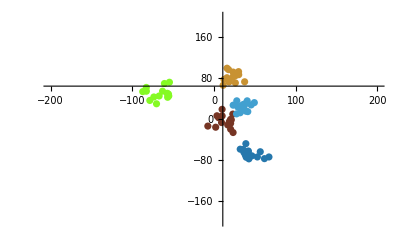

```mathematica
Show[Table[ListPlot[Style[X[[i]], RandomColor[]]],{i,1, k}], PlotRange->{2 range,2 range}]
```

```mathematica
initCentroids =  RandomReal[range,{k,2}]
```

{{-99.8458,-57.7923},{72.5811,49.2807},{50.1025,10.7381},{27.3704,11.6176},{-96.1045,-64.5251}}

```mathematica
assignCluster[centroids_]:=((Position[#, Min[#]] //Flatten)[[1]]&  @ (Norm /@(centroids- ConstantArray[#, Length[centroids]])))& /@ Flatten[X, 1]
```

```mathematica
calCentroids[clusterassignment_] :=Table[Mean[Flatten[X, 1][[Position[clusterassignment,i]//Flatten]  ]],{i, 1, k}]//fillMissingCentroids
```

```mathematica
fillMissingCentroids[centroids_] := ReplacePart[centroids,Thread[#->RandomReal[range,{Length[#], 2}]]]& @ (Position[centroids,Mean[__]]//Flatten)
```

```mathematica
cluster[centroids_] := cluster[centroids, ConstantArray[{0,0}, Length[centroids]]]
```

```mathematica
cluster[centroids_, prevCentroids_] :=centroids /; Fold[Plus, 0, Norm /@(prevCentroids-centroids)] ≤.1
```

```mathematica
cluster[centroids_, prevCentroids_] :=calCentroids[assignCluster[centroids]]  /; Fold[Plus, 0, Norm /@(prevCentroids-centroids)] >.1
```

```mathematica
clusters =cluster[initCentroids]
```

{{-79.2115,46.5955},{22.8996,83.5161},{45.9912,-45.7317},{2.85837,16.2417},{-31.0131,-86.9383}}

```mathematica
clusterAssignment =assignCluster[clusters]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

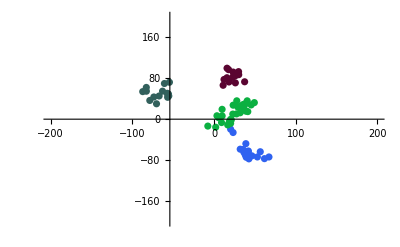

```mathematica
Show[Table[ListPlot[Style[ Flatten[X,1][[Position[clusterAssignment, i]//Flatten]], RandomColor[]]],{i,1,k}],PlotRange->{2 range,2 range}]
```